```mathematica
a=2;b=3;
```

```mathematica
Manipulate[ContourPlot[{1-(b+1)x+a*x^2y,b*x-a*x^2*y},{x,0,5},{y,0,5}],{a,0.1,10},{b,0.1,10}]
```

```mathematica
21-15
```

6

```mathematica
Manipulate[ContourPlot[{x*(b-x-y/(1+x))==0,y(x/(1+x)-a*y)==0},{x,-0.1,5},{y,-0.1,5}],{a,0.1,10},{b,0.1,10}]
```

```mathematica
aa=0.1; bb=3.1;
```

```mathematica
xPrime[x_,y_]:=x*(bb-x-y/(1+x)); yPrime[x_,y_]:=y(x/(1+x)-aa*y);
```

```mathematica
points1 = Table[{x,0},{x,-.1,5,0.2}];points2 = Table[{0,x},{x,-.1,5,0.2}]; points3 = Table[{x,(bb-x)(1+x)},{x,-.1,5,0.2}];points4 = Table[{x,x/(aa*(x+1))},{x,-.1,5,0.2}]; vectPoints = Join[points1,points2,points3,points4];
```

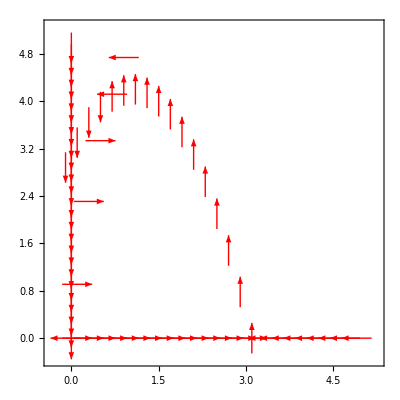

```mathematica
plt1 = VectorPlot[{0.5*xPrime[x,y]/Sqrt[xPrime[x,y]^2+yPrime[x,y]^2],0.5*yPrime[x,y]/Sqrt[xPrime[x,y]^2+yPrime[x,y]^2]},{x,-.1,5},{y,-.1,5},VectorPoints->vectPoints,VectorStyle->Red]
```

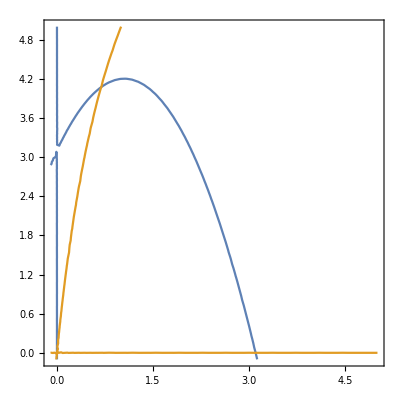

```mathematica
plt2 = ContourPlot[{x*(bb-x-y/(1+x))==0,y(x/(1+x)-aa*y)==0},{x,-0.1,5},{y,-0.1,5}]
```

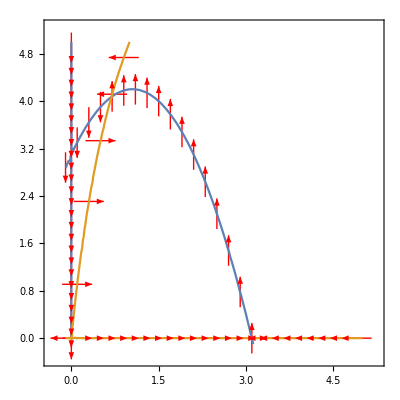

```mathematica
Show[plt1,plt2]
```

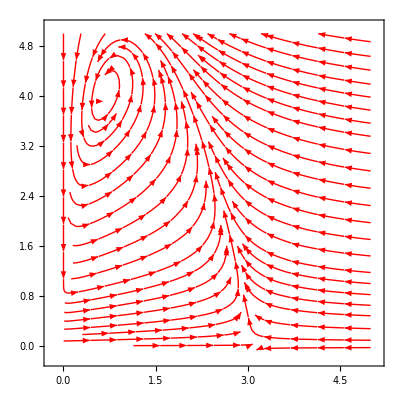

```mathematica
plt3 = StreamPlot[{x*(bb-x-y/(1+x)),y(x/(1+x)-aa*y)},{x,-0.1,5},{y,-0.1,5},StreamStyle->Red]
```

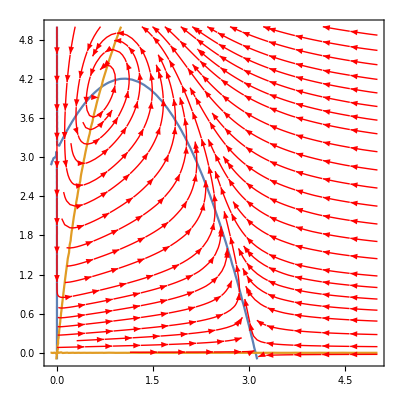

```mathematica
Show[plt2,plt3]
```

```mathematica
Manipulate[StreamPlot[{x*(b-x-y/(1+x)),y(x/(1+x)-a*y)},{x,0,5},{y,0,5}],{a,0.1,10},{b,0.1,10}]
```

```mathematica
Expand[a(b-x)(x+1)^2-x]
```

a b-x-a x+2 a b x-2 a x^2+a b x^2-a x^3

```mathematica
D[x(b-x-y/(x+1)),x]
```

b-x-y/(1+x)+x (-1+y/(1+x)^2)

```mathematica
D[x(b-x-y/(x+1)),y]
```

-x/(1+x)

```mathematica
D[y(x/(1+x)-a*y),x]
```

(-x/(1+x)^2+1/(1+x)) y

```mathematica
D[y(x/(1+x)-a*y),y]
```

x/(1+x)-2 a y

```mathematica
Simplify[(-x/(1+x)^2+1/(1+x)) y]
```

y/(1+x)^2

```mathematica
Manipulate[Show[ContourPlot[{x*(bb-x-y/(1+x))==0,y(x/(1+x)-aaa*y)==0},{x,-0.1,5},{y,-0.1,5}],StreamPlot[{x*(bb-x-y/(1+x)),y(x/(1+x)-aaa*y)},{x,-0.1,5},{y,-0.1,5},StreamStyle->Red]],{aaa,0.01,.1}]
```

```mathematica
acValue = 4(bb-2)/(bb^2*(bb+2))
```

0.0897758

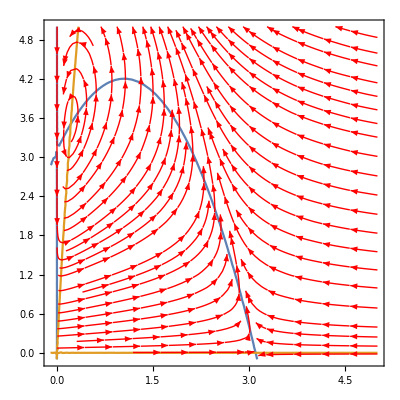

```mathematica
aaPre=0.05;Show[ContourPlot[{x*(bb-x-y/(1+x))==0,y(x/(1+x)-aaPre*y)==0},{x,-0.1,5},{y,-0.1,5}],StreamPlot[{x*(bb-x-y/(1+x)),y(x/(1+x)-aaPre*y)},{x,-0.1,5},{y,-0.1,5},StreamStyle->Red]]
```

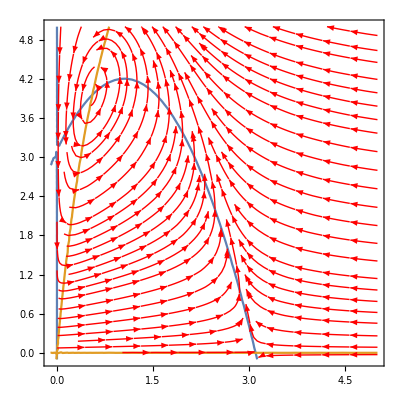

```mathematica
Show[ContourPlot[{x*(bb-x-y/(1+x))==0,y(x/(1+x)-acValue*y)==0},{x,-0.1,5},{y,-0.1,5}],StreamPlot[{x*(bb-x-y/(1+x)),y(x/(1+x)-acValue*y)},{x,-0.1,5},{y,-0.1,5},StreamStyle->Red]]
```

```mathematica
aaPost=0.1;Show[ContourPlot[{x*(bb-x-y/(1+x))==0,y(x/(1+x)-aaPost*y)==0},{x,-0.1,5},{y,-0.1,5}],StreamPlot[{x*(bb-x-y/(1+x)),y(x/(1+x)-aaPost*y)},{x,-0.1,5},{y,-0.1,5},StreamStyle->Red]]
```

-Graphics-